```mathematica
Integrate[Exp[2*sf]*Exp[-2*(Sin[t]^2)/Exp[2*l]], {t, 0, Pi}]/Pi
```

ⅇ^(-ⅇ^(-2 l)+2 sf) BesselI[0,ⅇ^(-2 l)]

```mathematica
D[Out[26], l]
```

2 ⅇ^(-ⅇ^(-2 l)-2 l+2 sf) BesselI[0,ⅇ^(-2 l)]-2 ⅇ^(-ⅇ^(-2 l)-2 l+2 sf) BesselI[1,ⅇ^(-2 l)]

```mathematica
Out[27]/.{l->Log[L]}
```

(2 ⅇ^(-1/L^2+2 sf) BesselI[0,1/L^2])/L^2-(2 ⅇ^(-1/L^2+2 sf) BesselI[1,1/L^2])/L^2

```mathematica
Out[28]/.{sf->Log[sf2]/2}
```

(2 ⅇ^(-1/L^2) sf2 BesselI[0,1/L^2])/L^2-(2 ⅇ^(-1/L^2) sf2 BesselI[1,1/L^2])/L^2

```mathematica
Out[26]/.{l->Log[L]}
```

ⅇ^(-1/L^2+2 sf) BesselI[0,1/L^2]

```mathematica
Out[30]/.{sf->Log[sf2]/2}
```

ⅇ^(-1/L^2) sf2 BesselI[0,1/L^2]

```mathematica
data=Table[Sin[30 2 Pi n/200]+(RandomReal[]-1/2),{n,200}];
```

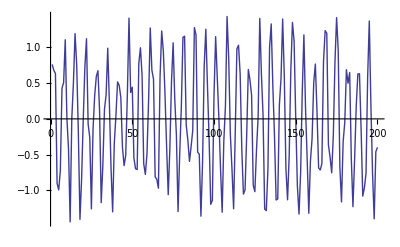

```mathematica
ListLinePlot[data]
```

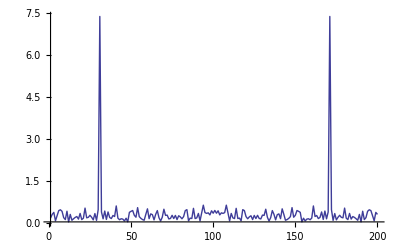

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->All]
```

```mathematica
Exp[-2*Sin[Pi*t/1]^2*(0.5^-2)]-Exp[-(0.5^-2)]*BesselI[0,0.5^-2]
```

-0.207002+ⅇ^(-8. Sin[π t]^2)

```mathematica
Denominator[ⅇ^(-2 Sin[π t]^2)]
```

ⅇ^(2 Sin[π t]^2)

```mathematica
data=Table[Out[102],{t,0,50,0.1}];
```

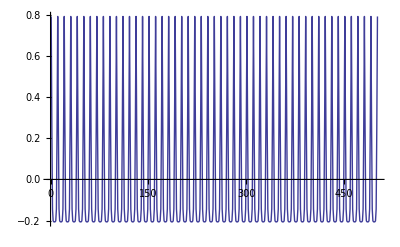

```mathematica
ListLinePlot[data]
```

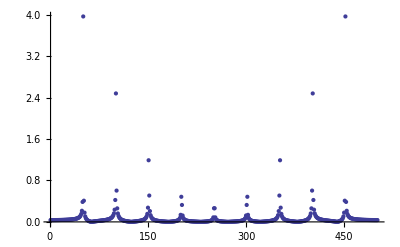

```mathematica
ListPlot[Abs[Fourier[data]], PlotRange->All]
```

```mathematica
Exp[2sf]*Exp[-2*(Sin[t]^2)/Exp[2*l]] - ⅇ^(-ⅇ^(-2 l)+2 sf) BesselI[0,ⅇ^(-2 l)]
```

ⅇ^(2 sf-2 ⅇ^(-2 l) Sin[t]^2)-ⅇ^(-ⅇ^(-2 l)+2 sf) BesselI[0,ⅇ^(-2 l)]

```mathematica
FullSimplify[ⅇ^(2 sf-2 ⅇ^(-2 l) Sin[t]^2)-ⅇ^(-ⅇ^(-2 l)+2 sf) BesselI[0,ⅇ^(-2 l)]]
```

ⅇ^(2 sf) (ⅇ^(-2 ⅇ^(-2 l) Sin[t]^2)-ⅇ^(-ⅇ^(-2 l)) BesselI[0,ⅇ^(-2 l)])

```mathematica
ⅇ^(2 sf) (ⅇ^(-2 ⅇ^(-2 l) Sin[t]^2)-ⅇ^(-ⅇ^(-2 l)) BesselI[0,ⅇ^(-2 l)])/(1-ⅇ^(-ⅇ^(-2 l)) BesselI[0,ⅇ^(-2 l)])
```

(ⅇ^(2 sf) (ⅇ^(-2 ⅇ^(-2 l) Sin[t]^2)-ⅇ^(-ⅇ^(-2 l)) BesselI[0,ⅇ^(-2 l)]))/(1-ⅇ^(-ⅇ^(-2 l)) BesselI[0,ⅇ^(-2 l)])

```mathematica
FullSimplify[(ⅇ^(2 sf) (ⅇ^(-2 ⅇ^(-2 l) Sin[π*t/Exp[p]]^2)-ⅇ^(-ⅇ^(-2 l)) BesselI[0,ⅇ^(-2 l)]))/(1-ⅇ^(-ⅇ^(-2 l)) BesselI[0,ⅇ^(-2 l)])]
```

(ⅇ^(2 sf) (ⅇ^(ⅇ^(-2 l) Cos[2 ⅇ^-p π t])-BesselI[0,ⅇ^(-2 l)]))/(ⅇ^(ⅇ^(-2 l))-BesselI[0,ⅇ^(-2 l)])

```mathematica
Out[11]/.{l->Log[L],sf->Log[sf2]/2,p->Log[P]}
```

(sf2 (ⅇ^(Cos[(2 π t)/P]/L^2)-BesselI[0,1/L^2]))/(ⅇ^(1/L^2)-BesselI[0,1/L^2])

```mathematica
FullSimplify[D[Out[11],p]]
```

(2 ⅇ^(-2 l-p+2 sf+ⅇ^(-2 l) Cos[2 ⅇ^-p π t]) π t Sin[2 ⅇ^-p π t])/(ⅇ^(ⅇ^(-2 l))-BesselI[0,ⅇ^(-2 l)])

```mathematica
Out[15]/.{l->Log[L],sf->Log[sf2]/2,p->Log[P]}
```

(2 ⅇ^(Cos[(2 π t)/P]/L^2) π sf2 t Sin[(2 π t)/P])/(L^2 P (ⅇ^(1/L^2)-BesselI[0,1/L^2]))

```mathematica
FullSimplify[D[Out[11],l]]
```

-(2 ⅇ^(-2 l+2 sf) ((-ⅇ^(ⅇ^(-2 l))+ⅇ^(ⅇ^(-2 l) Cos[2 ⅇ^-p π t])) BesselI[1,ⅇ^(-2 l)]+BesselI[0,ⅇ^(-2 l)] (ⅇ^(ⅇ^(-2 l))-ⅇ^(ⅇ^(-2 l) Cos[2 ⅇ^-p π t]) Cos[2 ⅇ^-p π t])-2 ⅇ^(2 ⅇ^(-2 l) Cos[ⅇ^-p π t]^2) Sin[ⅇ^-p π t]^2))/((ⅇ^(ⅇ^(-2 l))-BesselI[0,ⅇ^(-2 l)])^2)

```mathematica
Out[14]/.{l->Log[L],sf->Log[sf2]/2,p->Log[P]}
```

-(2 sf2 ((-ⅇ^(1/L^2)+ⅇ^(Cos[(2 π t)/P]/L^2)) BesselI[1,1/L^2]+BesselI[0,1/L^2] (ⅇ^(1/L^2)-ⅇ^(Cos[(2 π t)/P]/L^2) Cos[(2 π t)/P])-2 ⅇ^((2 Cos[(π t)/P]^2)/L^2) Sin[(π t)/P]^2))/(L^2 (ⅇ^(1/L^2)-BesselI[0,1/L^2])^2)

```mathematica
(ⅇ^(2 sf) (ⅇ^(ⅇ^(-2 l) Cos[2 ⅇ^-p π t])-BesselI[0,ⅇ^(-2 l)]))/(ⅇ^(ⅇ^(-2 l))-BesselI[0,ⅇ^(-2 l)]) - ⅇ^(2 sf) *Cos[2*Exp[-p]*π*t]
```

(ⅇ^(2 sf) (ⅇ^(ⅇ^(-2 l) Cos[2 ⅇ^-p π t])-BesselI[0,ⅇ^(-2 l)]))/(ⅇ^(ⅇ^(-2 l))-BesselI[0,ⅇ^(-2 l)])-ⅇ^(2 sf) Cos[2 ⅇ^-p π t]

```mathematica
FullSimplify[(ⅇ^(2 sf) (ⅇ^(ⅇ^(-2 l) Cos[2 ⅇ^-p π t])-BesselI[0,ⅇ^(-2 l)]))/(ⅇ^(ⅇ^(-2 l))-BesselI[0,ⅇ^(-2 l)])-ⅇ^(2 sf) Cos[2 ⅇ^-p π t]]
```

ⅇ^(2 sf) ((ⅇ^(ⅇ^(-2 l) Cos[2 ⅇ^-p π t])-BesselI[0,ⅇ^(-2 l)])/(ⅇ^(ⅇ^(-2 l))-BesselI[0,ⅇ^(-2 l)])-Cos[2 ⅇ^-p π t])